```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian System eta Data\\beta_0.06_NM_eta_vary"];
LNDataeta001=ReadList["LNData_NM_eta_0.01_oOmega_Resonance.txt"];
LNDataeta002=ReadList["LNData_NM_eta_0.02_oOmega_Resonance.txt"];
LNDataeta003=ReadList["LNData_NM_eta_0.03_oOmega_Resonance.txt"];
LNDataeta004=ReadList["LNData_NM_eta_0.04_oOmega_Resonance.txt"];
LNDataeta005=ReadList["LNData_NM_eta_0.05_oOmega_Resonance.txt"];
LNDataeta006=ReadList["LNData_NM_eta_0.06_oOmega_Resonance.txt"];
LNDataeta007=ReadList["LNData_NM_eta_0.07_oOmega_Resonance.txt"];
```

```mathematica
eta001=Table[Table[{LNDataeta001[[pair]][[pt]][[1]], 0.01, LNDataeta001[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
eta002=Table[Table[{LNDataeta002[[pair]][[pt]][[1]], 0.02, LNDataeta002[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
eta003=Table[Table[{LNDataeta003[[pair]][[pt]][[1]], 0.03, LNDataeta003[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
eta004=Table[Table[{LNDataeta004[[pair]][[pt]][[1]], 0.04, LNDataeta004[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
eta005=Table[Table[{LNDataeta005[[pair]][[pt]][[1]], 0.05, LNDataeta005[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
eta006=Table[Table[{LNDataeta006[[pair]][[pt]][[1]], 0.06, LNDataeta006[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
eta007=Table[Table[{LNDataeta007[[pair]][[pt]][[1]], 0.07, LNDataeta007[[pair]][[pt]][[2]]}, {pt, 1, 1001}], {pair, 1, 6}];
```

```mathematica
(* LN12, LN13=LN24, LN14=LN23, LN34 *)
etaData={
{eta001[[1]], eta001[[2]], eta001[[3]], eta001[[6]]},
{eta002[[1]], eta002[[2]], eta002[[3]], eta002[[6]]},
{eta003[[1]], eta003[[2]], eta003[[3]], eta003[[6]]},
{eta004[[1]], eta004[[2]], eta004[[3]], eta004[[6]]},
{eta005[[1]], eta005[[2]], eta005[[3]], eta005[[6]]},
{eta006[[1]], eta006[[2]], eta006[[3]], eta006[[6]]},
{eta007[[1]], eta007[[2]], eta007[[3]], eta007[[6]]}};
(* Modified Data Order: LN34, LN12, LN14=LN23, LN13=LN24*)
etaData={
{eta001[[6]], eta001[[1]], eta001[[3]],eta001[[2]]},
{eta002[[6]], eta002[[1]], eta002[[3]], eta002[[2]]},
{eta003[[6]], eta003[[1]], eta003[[3]],eta003[[2]]},
{eta004[[6]], eta004[[1]], eta004[[3]],eta004[[2]]},
{eta005[[6]], eta005[[1]], eta005[[3]],eta005[[2]]},
{eta006[[6]], eta006[[1]], eta006[[3]],eta006[[2]]},
{eta007[[6]], eta007[[1]], eta007[[3]],eta007[[2]]}};
```

```mathematica
PlotFormat={PlotRange->{{0, 500}, {0.01, 0.07}, {0, 3}}, Filling->Bottom, PlotStyle->Directive[PointSize->0.002], AxesLabel->{"τ", "η", "𝒩"}, LabelStyle->Directive[Black, FontSize->20, FontFamily->"Latin Modern Roman"], Ticks->{Table[time, {time, 0, 500, 100}], Table[eta, {eta, 0, 0.07, 0.01}], Automatic}};
ListPointPlot3D[etaData[[7]], Evaluate[PlotFormat]];

PlotFormat={PlotRange->{{0, 500}, {0.01, 0.07}, {0, 3.1}}, Filling->Bottom, PlotStyle->{Directive[Red, Thickness[0.0020]], Directive[Lighter[Blue], Thickness[0.0020]], Directive[Darker[Green], Thickness[0.0020]], Directive[Yellow, Thickness[0.0030]]}, AxesLabel->{"τ", "η", "𝒩"}, LabelStyle->Directive[Black, FontSize->20, FontFamily->"Latin Modern Roman"], Ticks->{Table[time, {time, 0, 500, 100}], Table[eta, {eta, 0, 0.07, 0.01}], Automatic}, BoxRatios->{3.5, 3.5,0.7}};
ListLinePlot3D[etaData[[7]], Evaluate[PlotFormat]]
```

-Graphics3D-

```mathematica
etaplots=Table[ListLinePlot3D[etaData[[n]], Evaluate[PlotFormat]], {n, 1, 7}];
NonMarkovianSystemEta=Rasterize[Show[etaplots, ImageSize->Large, ViewPoint->{2, -2.5, 2.5}]]
```

-Graphics-

```mathematica
Export["Non-Markovian System Eta_oOmega_Resonance.png",NonMarkovianSystemEta]
```

Non-Markovian System Eta_oOmega_Resonance.png

```mathematica
GetPeaks[Data_]:=Module[{Output},
Output={};
Table[If[Data[[pt]][[2]]>Data[[pt-5]][[2]]&&Data[[pt]][[2]]>Data[[pt+5]][[2]]&&Data[[pt]][[2]]>Data[[pt-4]][[2]]&&Data[[pt]][[2]]>Data[[pt+4]][[2]]&&Data[[pt]][[2]]>Data[[pt-3]][[2]]&&Data[[pt]][[2]]>Data[[pt+3]][[2]]&&Data[[pt]][[2]]>Data[[pt-2]][[2]]&&Data[[pt]][[2]]>Data[[pt+2]][[2]]&&Data[[pt]][[2]]>Data[[pt-1]][[2]]&&Data[[pt]][[2]]>Data[[pt+1]][[2]], AppendTo[Output, Data[[pt]]]], {pt, 6, Length[Data]-5}];
Return[Sort[Output]];
]
PeakData=GetPeaks[Join[LNDataeta007[[1]], LNDataeta007[[6]]]];
KeepPeaks={};
Table[If[PeakData[[pt]][[2]]>1.5, AppendTo[KeepPeaks, PeakData[[pt]]]], {pt, 1, Length[PeakData]}];
EnvelopFunc=Interpolation[KeepPeaks];
```

```mathematica
(* Plot Formatting *)
Title="Non-Markovian System: {n=4, β=0.06, η=0.07, m=1, ω=1, Ω=1, γ=0.5}"; 
height=400;
width=1000;
PlotFormat={Joined->True, PlotRange->{0, 3}, ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"τ", "𝒩"}, AxesStyle->Directive[Black,23], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 25], PlotLabel->None, PlotStyle->{Thickness[0.0010]}};
(* Plot LN Data of the System *)
LNPlot=ListPlot[{LNDataeta007[[1]], LNDataeta007[[2]], LNDataeta007[[3]], LNDataeta007[[6]]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->Bottom];

(* Data order should be LN34 (Red), LN12 (Blue), LN14=LN23 (Green), LN13=LN24 (Yellow) *)
LNPlot2=ListLinePlot[{LNDataeta007[[6]], LNDataeta007[[1]], LNDataeta007[[3]], LNDataeta007[[2]]}, PlotStyle->{Directive[Red, Thickness[0.0010]], Directive[Lighter[Blue], Thickness[0.0010]], Directive[Darker[Green], Thickness[0.0010]], Directive[Yellow, Thickness[0.0020]]}, Evaluate[PlotFormat], (* PlotLegends->{"LN12", "LN13 = LN24", "LN14 = LN23", "LN34"},*) Filling->Bottom];

(* Data order should be LN34 (Red), LN12 (Blue), LN14=LN23 (Green), LN13=LN24 (Yellow) *)

LNPLotwithEnvelopFunc=Rasterize[Show[LNPlot2, Plot[EnvelopFunc[x], {x, 0.5, 482}, PlotStyle->Directive[Black], PlotRange->All]]]
```

InterpolatingFunction::dmval: Input value {0.509836} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
Export["Non-Markovian System Eta 0.07_oOmega_Resonance.png", LNPLotwithEnvelopFunc]
```

Non-Markovian System Eta 0.07_oOmega_Resonance.png

```mathematica
(* Load Resonance and non-Resonance Case for t = 0 to 4000 *)
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian System eta Data\\beta_0.06_NM_eta_vary\\eta_0.07_t_0_long_time"];
LongTimeNoRes=ReadList["LNData_NM_eta_0.07_t_0_4000.txt"];
LongTimeRes=ReadList["C:\\Users\\physk\\OneDrive\\Desktop\\Non-Markovian System eta Data\\beta_0.06_NM_eta_vary\\eta_0.07_t_0_long_time\\LNData_NM_beta_0.06Oomega_Resonant_Long_Time.txt"];
```

```mathematica
(* Resonance Plot and Enveloping Function *)
ResPeaks=GetPeaks[Join[LongTimeRes[[1]], LongTimeRes[[6]]]];
KeepResPeaks={};
Table[If[ResPeaks[[pt]][[2]]>1, AppendTo[KeepResPeaks, ResPeaks[[pt]]]], {pt, 1, Length[ResPeaks]}];
EnvFuncRes=ListPlot[KeepResPeaks, PlotStyle->Directive[Gray], Evaluate[PlotFormat]];

(* non-Resonance Plot and Enveloping Function *)
nonResPeaks=GetPeaks[Join[LongTimeNoRes[[1]], LongTimeNoRes[[6]]]];
KeepnonResPeaks={};
Table[If[nonResPeaks[[pt]][[2]]>0.85, AppendTo[KeepnonResPeaks, nonResPeaks[[pt]]]], {pt, 1, 59}];
Table[If[nonResPeaks[[pt]][[2]]>0, AppendTo[KeepnonResPeaks, nonResPeaks[[pt]]]], {pt, 60, Length[nonResPeaks]}];
EnvFuncnonRes=ListPlot[KeepnonResPeaks, PlotStyle->Directive[Gray], Evaluate[PlotFormat]];
```

```mathematica
(* Interpolation Functions *)
IFuncRes=Interpolation[KeepResPeaks]
IFuncnonRes=Interpolation[KeepnonResPeaks]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
height=400;
width=600;
PlotFormat2={PlotRange->{0, 3}, ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"τ", "𝒩"}, AxesStyle->Directive[Black,23], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 25], PlotLabel->None, PlotStyle->{Thickness[0.0010]}};

EnvFuncPlots=Plot[{IFuncnonRes[x], IFuncRes[x]}, {x, 1, 4000}, PlotStyle->{Directive[Gray, Dashed, Thick], Directive[Black, Thick]}, Evaluate[PlotFormat2]];

ResPlot=ListLinePlot[{LongTimeRes[[6]][[1;;8001]], LongTimeRes[[1]][[1;;8001]]}, PlotStyle->{Directive[Red, Thickness[0.0010]], Directive[Lighter[Blue], Thickness[0.0010]]}, Evaluate[PlotFormat2], Filling->Bottom];

nonResPlot=ListLinePlot[{LongTimeNoRes[[6]][[1;;8001]], LongTimeNoRes[[1]][[1;;8001]]}, PlotStyle->{Directive[Red, Thickness[0.0010]], Directive[Lighter[Blue], Thickness[0.0010]]}, Evaluate[PlotFormat2], Filling->Bottom];

LongTime=Rasterize[Show[EnvFuncPlots]]
```

-Graphics-

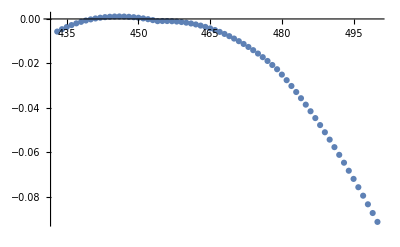

```mathematica
ListPlot[Table[{x, IFuncnonRes[x]-IFuncRes[x]}, {x, 433, 500}]]
```

```mathematica
{452, IFuncnonRes[452]}
{452, IFuncRes[452]}
```

{452,1.82456}

{452,1.82467}

```mathematica
Table[{x, IFuncRes[x+1]-IFuncRes[x]}, {x, 158, 165}]//MatrixForm
```

(158 | -0.000611031
159 | -0.00047671
160 | 0.000464672
161 | 0.000590531
162 | 0.000709532
163 | 0.000821676
164 | 0.000926962
165 | 0.00102539)

```mathematica
IFuncRes[159]
IFuncRes[160]
IFuncRes[161]
```

1.54309

1.54261

1.54308

```mathematica
Export["Resonance versus nonResonance.png", LongTime]
```

Resonance versus nonResonance.png